```mathematica
Get["invariant_dmd_v2_8_functions"];
Get["invariant_dmd_v2_8_auxuntested_v1"];
```

```mathematica
Get["dslibrary_v3_3"];
```

## Savefile

```mathematica
savefile = "duffing_spiral_pruned_v1";
```

## Temporal parameters

0 usually - If delayed, set appropriately

```mathematica
ndelays = 0;

tinit = 0;
tsamp = 1.6;
```

#### Choice of DS

```mathematica
(* Create a separate one for each DS*)
alphabetadelta = {-1,6^2(*Use to shift the fixed points : n^2*),1 (*Closer to 0, greater the swirl*)};
localduffing[t_,r_]:=duffing[t,r,alphabetadelta];


vfield = localduffing;
(* Did not know a better way to do ICs without distrubing the code that follows *)

(* chosenputty: Use to convert coordinates from the ODE version *)
chosenputty =#& ;
```

### Tolerances

```mathematica
(* Tolerance *)
sigtols = {10^-8,10^-12}; (* Singular values *)
restols = {10^-8,10^-12};(* greaterabsrelcheck *)
```

### Flavours

Switches for the constant eigenfunction && the delay constraints (You need to put the constant function in userhead !!!) : Set True to activate

#### User defined functions

```mathematica
(* AppendTo[userlist,(*Desired fheads*)];*)
userparams = {};
```

#### User defined constraints

Should be a LIST of matrices !!!

```mathematica
(* Geometric constraints *)
invsamplesets ;
(* Functional constraints *)
ipfuns(**);
opfuns(**);
rawuserlist = {};
```

#### Test constraints

```mathematica
testinvsamplesets=N@getduffinginvsamplesets[alphabetadelta];
testipfuns;
testopfuns;
```

```mathematica
boxranges = {{-1,1},{-1,1}};
centercounts = {{35,35},{9,9}(* Must be the same as the first to ensure that the scaling is correctly done for trigtri *)};
nsampsperbox = {5,5};
flavour = "boxfuns";


(* How muich of the fringe be included in the plots*)
plotscalefactor = 1.1;
```

## Must use this version !!!!

```mathematica
icsconwrap4modifiedoneshot[ics_,{{construct_,basistruct_,invsamplesets_,testinvsamplesets_},{userparams_,rawuserlist_,ipfuns_,opfuns_,testipfuns_,testopfuns_}}]:=modifiedoneshot[ndelays,tinit,tsamp,vfield,ics,chosenputty,sigtols,restols,flavour,flavourparams,construct,basistruct,userparams,rawuserlist,invsamplesets,ipfuns,opfuns,testinvsamplesets,testipfuns,testopfuns,boxflavourparams];
```

## Actual test

#### Sample points

```mathematica
boxflavourparams = {boxranges,centercounts[[-1]]};
flavourparams ={boxranges,centercounts[[1]]};
```

```mathematica
detics = N@Join@@MapThread[(#1@(getdetseeds4Box[boxranges,#2,#3]))&,{{#&,puttheseoutright[#,boxflavourparams]&},centercounts,nsampsperbox}];
ncompsamples = Length@detics;
```

#### Plot points

```mathematica
plotcc = centercounts[[1]];
plotspb = nsampsperbox[[1]];
plotbrs  = plotscalefactor *boxranges;
plotparams = {plotbrs,plotcc,plotspb};
(*----------ODE in sampled coordinates ----------*)
plotics = N@getdetseeds4Box@@plotparams;
```

### Le test variations

#### Expected spectrum

```mathematica
jacobevals =FunctionExpand@Flatten@Map[N@Eigenvalues@getjacobian[(*Vector field *)vfield,{t,#}]&,(*fixedpoints*)Flatten[testinvsamplesets,1]];
expectedevalues  = Exp[jacobevals*tsamp];
```

```mathematica
neededbaggage = {detics,plotics,sigtols,tsamp,ncompsamples,ndelays,flavourparams,expectedevalues};
```

```mathematica
activecons;
passivecons = {userparams,rawuserlist,ipfuns,opfuns,testipfuns,testopfuns};
```

```mathematica
Print[{centercounts,nsampsperbox}];
goodplotgrub=MapThread[getcrunchedata[{#1,#2,#3,testinvsamplesets},passivecons,neededbaggage]&,{{True,True,False},{True,True,False},{testinvsamplesets,{},{}}}];
DumpSave[savefile,{goodplotgrub,plotparams}];
```

{{{35,35},{9,9}},{5,5}}

{1.6,32561,0,{{{-1,1},{-1,1}},{35,35}},{10.4878,0},{{1.69352×10^-15,4.99517×10^-14},{2.36468×10^-15,2.36468×10^-15}},1689.36}

{1.6,32561,0,{{{-1,1},{-1,1}},{35,35}},{10.5431,0},{{0.350945,9.12316},{1.62026×10^-15,1.62026×10^-15}},1688.74}

{1.6,32561,0,{{{-1,1},{-1,1}},{35,35}},{1.,0},{{0.351726,9.12316},{}},1688.74}

```mathematica
Quit[];
```

### Plots

```mathematica
(* Also fetch all functions in auxuntested_v1 *)
Get["invariant_dmd_v2_8_functions"];
Get["invariant_dmd_v2_8_auxuntested_v1"];
(* Typically file name is stored in savefile *)
Get["duffing_spiral_pruned_v1"];
```

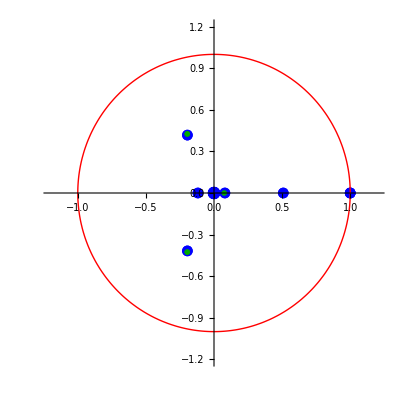
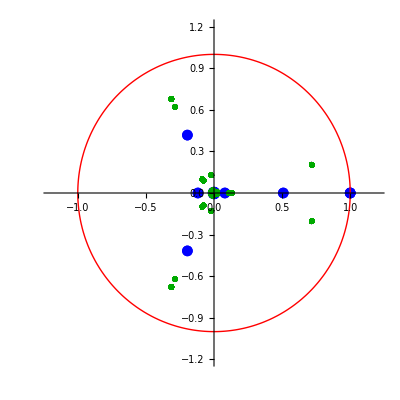

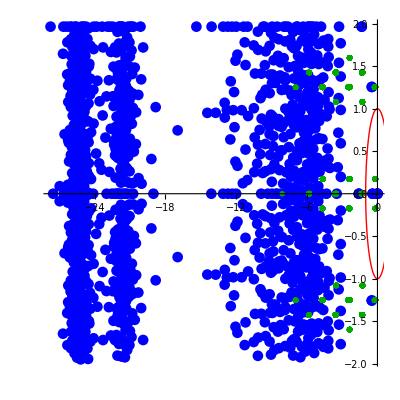

```mathematica
visualizespectrum [goodplotgrub[[1]],plotparams];
```

```mathematica
plotics = N@getdetseeds4Box@@plotparams;
```

```mathematica
{ploticslifted,testefgrubvecs} = goodplotgrub[[1,{2,3}]];
```

```mathematica
Table[ListDensityPlot[getlistplotdata[testefgrubvecs[[i,1]],N@plotics,ploticslifted,Abs],PlotRange->All,PerformanceGoal->"Quality",PlotLegends->Automatic,LabelStyle->Directive[Black, Medium]],{i,3}]
```

{-Graphics-,-Graphics-,-Graphics-}